### Load and process data

```mathematica
$HistoryLength=0;
```

```mathematica
importReal64MultiList[dir_,template_]:=Module[{filenameTemplate,depth,dimensions,imported},
filenameTemplate=StringTemplate[template];
depth=StringCount[template,"``"];
dimensions=(Length[FileNames[#,dir,1]]&)@*(TemplateApply[filenameTemplate,Table[If[i==#,"*",0],{i,depth}]]&)/@Range[depth];
imported=Array[Import[dir<>filenameTemplate[##],"Real64"]&,dimensions,ConstantArray[0,depth]];
{dimensions,imported}
];
```

```mathematica
importReal64MultiListTemp[dir_,template_]:=Module[{filenameTemplate,depth,dimensions,imported},
filenameTemplate=StringTemplate[template];
depth=StringCount[template,"``"];
dimensions=(Length[FileNames[#,dir,1]]&)@*(TemplateApply[filenameTemplate,Table[If[i==#,"*",0],{i,depth}]]&)/@Range[depth];
(*imported=Array[Import[dir<>filenameTemplate[##],"Real64"]&,dimensions,ConstantArray[0,depth]];
{dimensions,imported}*)
dimensions
];
```

```mathematica
importSetup[paramNames_,paramTypes_,dir_,setupFilename_]:=AssociationThread[paramNames->Import[dir<>setupFilename,"Binary","DataFormat"->paramTypes][[1]]];
```

```mathematica
(*dir=NotebookDirectory[]<>"output/initial_test/";*)
(*dir="/home/hypermania/Research/BHQuasinormalMode/output/initial_test/";*)
dir="/home/hypermania/Research/BHQuasinormalModes/output/faraway_test/";
(*dir="/home/hypermania/Research/BHQuasinormalModes/output/single_idx_test/";*)
paramNames=Import[dir<>"paramNames.txt","List"];
paramTypes=Import[dir<>"paramTypes.txt","List"];
param=importSetup[paramNames,paramTypes,dir,"param.dat"]
```

<|s→2,l→2,r0→1.,r_min→-200.,r_max→200.,N→4096|>

```mathematica
rList=Table[param["r_min"]+(param["r_max"]-param["r_min"])/(param["N"]-1)(i-1/2),{i,0,param["N"]}];
```

```mathematica
tList[[-1]]/Length[tList]/((param["r_max"]-param["r_min"])/(param["N"]-1))
```

Part::partd: Part specification tList⟦-1⟧ is longer than depth of object.

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
tList=importReal64MultiList[dir,"t_list.dat"][[2]];
stateList=importReal64MultiList[dir,"state_``.dat"][[2]];
ψList=(#[[1;;param[["N"]]+1]]&)/@stateList;
dtψList=(#[[param[["N"]]+2;;-1]]&)/@stateList;
ClearAll[stateList];
```

```mathematica
(*tList=importReal64MultiList[dir,"t_list.dat"][[2]];
ψSingleList=importReal64MultiList[dir,"psi_list.dat"][[2]];
dtψSingleList=importReal64MultiList[dir,"dt_psi_list.dat"][[2]];*)
```

Import::nffil: File /home/hypermania/Research/BHQuasinormalModes/output/faraway_test/psi_list.dat not found during Import.

Import::nffil: File /home/hypermania/Research/BHQuasinormalModes/output/faraway_test/dt_psi_list.dat not found during Import.

```mathematica
tToIdx[t_]:=FirstPosition[tList,_?(#>t&)][[1]];
rToIdx[r_]:=FirstPosition[rList,_?(#>r&)][[1]];
```

```mathematica
Manipulate[ListPlot[{rList,ψList[[i]]}ᵀ,Joined->True,PlotRange->{All,{-0.5,0.5}},ImageSize->Large,AxesLabel->{"r_*","ψ"},Epilog->{Text[Style[StringTemplate["t=``"][tList[[i]]],24],{-50,0.4}]}],{i,1,Length[tList],1}]
```

```mathematica
(*Manipulate[ListPlot[{rList,ψList[[i]]}ᵀ,Joined->True,PlotRange->{{0,20},{-0.5,0.5}},ImageSize->Large,AxesLabel->{"r_*","ψ"},PerformanceGoal->"Quality",Epilog->{Text[Style[StringTemplate["t=``"][tList[[i]]],24],{-50,0.4}]}],{i,{19000}}]*)
```

```mathematica
(*ListPlot[{tList,ψList[[All,rToIdx[150]]]}ᵀ,Joined->True,PlotRange->{All,All}]*)
```

### Extracting QNM modes

#### Position of peak of potential

```mathematica
f[r_]:=1-r0/r;
V[r_]:=f[r]((l(l+1))/r^2+(1-s^2)((2M)/r^3))/.(M->(d-2)A r0^(d-3)/(16π)/.A->2 π^((d-1)/2)/Gamma[(d-1)/2]/.d->4);
rSoln=DSolve[1-r0/r[rast]==r'[rast],r,rast][[1]]/.C[1]->0;
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
subs={s->param["s"],r0->param["r0"],l->param["l"]};
```

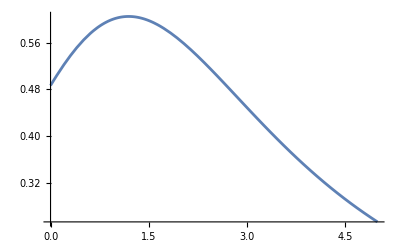

```mathematica
Plot[Evaluate[V[r[rast]/.rSoln]/.subs],{rast,0,5}]
```

```mathematica
Vexpr=Evaluate[V'[r[rast]/.rSoln]/.subs]//Simplify
```

(3.+3. ProductLog[0.367879 ⅇ^(1. rast)]-12. ProductLog[0.367879 ⅇ^(1. rast)]^2)/((1.+ProductLog[0.367879 ⅇ^(1. rast)])^5)

```mathematica
rPeak=rast/.FindRoot[Vexpr,{rast,1}]
```

1.19471

#### Fitting

```mathematica
tIdxMin=tToIdx[110];
tIdxMax=tToIdx[150];
tFitMin=tList[[tIdxMin]];
tFitMax=tList[[tIdxMax]];
rIdx=rToIdx[50];
rEval=rList[[rIdx]];
```

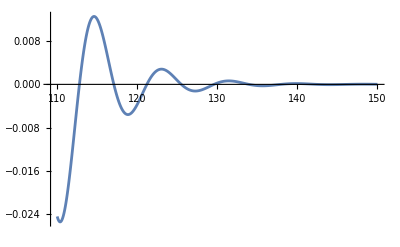

```mathematica
dat={tList,ψList[[All,rIdx]]}ᵀ[[tIdxMin;;tIdxMax]];
ListPlot[dat,Joined->True,PlotRange->{All,All}]
```

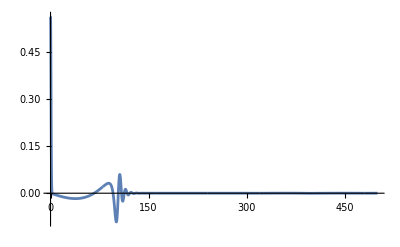

```mathematica
ListPlot[{tList,ψList[[All,rIdx]]}ᵀ,Joined->True,PlotRange->Full]
```

```mathematica
(*ListLogPlot[Abs[dat],Joined->True]*)
```

```mathematica
(*expr=A ⅇ^(-ωI(t-tFitMin))Cos[ωR(t-tFitMin)+θ];
fit=FindFit[dat,{expr,0<A<1,ωI<1,ωI>0,ωR<10,ωR>0,θ>0,θ<2π},{A,ωI,ωR,θ},t,Method->"NMinimize"]
fittedDat=Table[{t,expr}/.fit,{t,tFitMin,tFitMax,0.05}];*)
```

```mathematica
(*ListLinePlot[{dat,fittedDat},PlotRange->Full]*)
```

#### From literature (Spectral decomposition of the perturbation response of the Schwarzschild geometry)

```mathematica
sList={-0.17792-0.74734I,-0.54783-0.69342I,-0.95655-0.60211I,-1.41030 -0.50301I,-1.89369 -0.41503I,-2.39122-0.33860I,-2.89582-0.26650I};
BList={0.12690+0.02032I,0.04768-0.22376I,-0.19028+0.01575I,0.08087+0.07961I,-0.01710-0.06053I,-0.00169+0.03643I,0.01067-0.02741I};
qnm22Expr=∑_(i=1)^Length[BList] BList[[i]]Exp[sList[[i]](t-(rSource+rEval-2rPeak))]/.rSource->50;
```

```mathematica
expr=Re[A qnm22Expr]/.t->t-tShift;
fit=FindFit[dat,{expr,-3<tShift<3},{A,tShift},t,Method->"NMinimize"]
fittedDat=Table[{t,expr}/.fit,{t,tFitMin,tFitMax,0.05}];
```

```mathematica
expr=Re[A qnm22Expr];
fit=FindFit[dat,{expr},{A},t,Method->"NMinimize"]
fittedDat=Table[{t,expr}/.fit,{t,tFitMin,tFitMax,0.05}];
```

FindFit::lmnl: The model Re[A («8»+(0.04768-0.22376 ⅈ) ⅇ^((-«8»-«1») «1»)+(0.1269+0.02032 ⅈ) ⅇ^((-0.17792-0.74734 ⅈ) (-97.6228+t)))] is linear in the parameters {A}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

{A→1.99023}

```mathematica
unfittedDat=Table[{t,expr}/.{tShift->0,A->3.5},{t,tFitMin,tFitMax,0.05}];
```

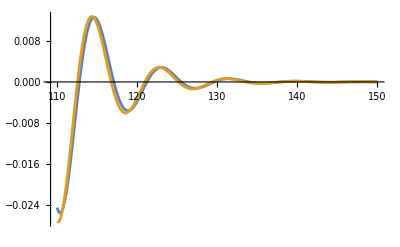

```mathematica
ListLinePlot[{dat,fittedDat},PlotRange->Full,Joined->True]
```

```mathematica
fittedDat=Table[{t,expr}/.fit,{t,tFitMin,499,0.05}];
```

General::munfl: (0.01067-0.02741 ⅈ) (-1.65465×10^-306-5.89852×10^-306 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (0.01067-0.02741 ⅈ) (-1.49949×10^-306-5.08389×10^-306 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (0.01067-0.02741 ⅈ) (-1.35585×10^-306-4.38092×10^-306 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
ψInterpolant=Interpolation[{{#[[1]]},#[[2]],#[[3]]}&/@({tList,ψList[[All,rIdx]],dtψList[[All,rIdx]]}ᵀ)];
ψFittedInterpolant=Interpolation[fittedDat];
```

```mathematica
ψInterpolant2=Interpolation[{{#[[1]]},#[[2]],#[[3]]}&/@({tList,ψSingleList,dtψSingleList}ᵀ)];
```

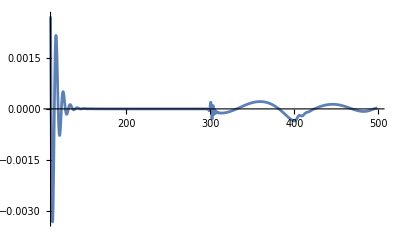

```mathematica
Plot[ψInterpolant[t]-ψFittedInterpolant[t],{t,tFitMin,499},PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {110.003} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

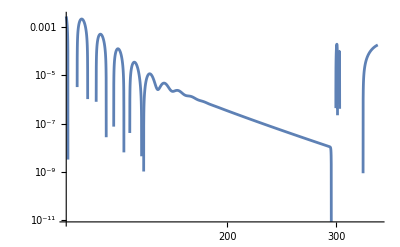

```mathematica
LogLogPlot[ψInterpolant[t]-ψFittedInterpolant[t],{t,110,350},PlotRange->Full]
```

```mathematica
tList[[-1]]
```

2000.

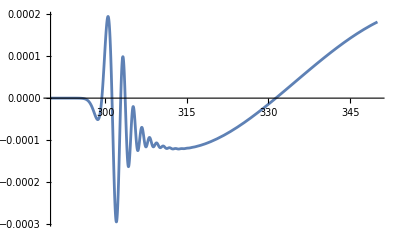

```mathematica
Plot[ψInterpolant2[t],{t,290,350},PlotRange->{All,All}]
```

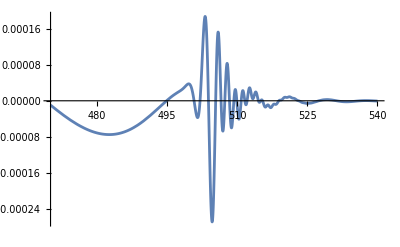

```mathematica
Plot[ψInterpolant2[t],{t,470,540},PlotRange->{All,All}]
```

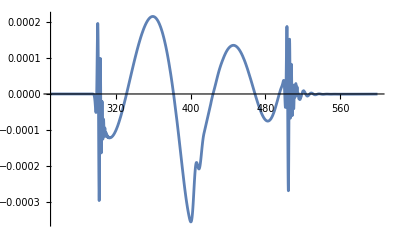

```mathematica
Plot[ψInterpolant2[t],{t,250,600},PlotRange->{All,All}]
```

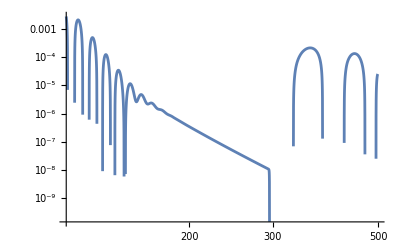

```mathematica
LogLogPlot[ψInterpolant[t]-ψFittedInterpolant[t],{t,tFitMin,499},PlotRange->Full]
```

```mathematica
rIdx
```

2561

```mathematica
param
```

<|s→2,l→2,r0→1.,r_min→-200.,r_max→200.,N→4096|>

```mathematica
rEval
```

50.0122

```mathematica
diffψ[t_]:=ψInterpolant[t]-ψFittedInterpolant[t];
```

```mathematica
(Log[diffψ[t2]]-Log[diffψ[t1]])/(Log[t2]-Log[t1])/.{t1->200,t2->249}
```

-9.21537

```mathematica
-2*2-3
```

-7

late time decay tail

```mathematica
(*(2ν+1)!!(ⅈ s)^(-ν-1)(1-r^-1)^s CoulombF[ν,-ⅈ s,ⅈ s r]*)
```

```mathematica
f=(-1)^(l+1)(2(2l+2)!)/((2l+1)!!)^2(r rP)^(l+1)(t-tP)^(-2l-3)/.{tP->0,rP->50,l->2,r->100}
```

-800000000000/t^7

```mathematica
f=(-1)^(l+1)((2l+2)!)/((2l+1)!!)rP^(l+1)(t-tP-rP)^(-l-2)/.{tP->0,rP->50,l->2}
```

-6000000/(-50+t)^4

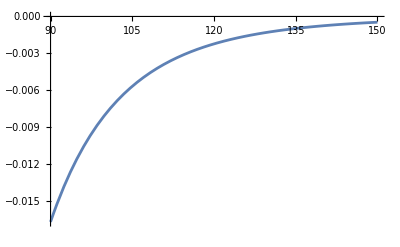

```mathematica
Plot[f,{t,90,150}]
```

```mathematica
Limit[CoulombF[l,-ⅈ s,ⅈ s r]/Sin[ⅈ s r-l π/2],s->0]
```

0

## Scratch

```mathematica
(*expr2=A1 ⅇ^(-ωI1(t-tFitMin))Cos[ωR1(t-tFitMin)+θ1]+A2 ⅇ^(-ωI2(t-tFitMin))Cos[ωR2(t-tFitMin)+θ2];
fit2=FindFit[dat,{expr2,0<A1<1,0<ωI1<1,0<ωR1<10,0<θ1<2π,0<A2<1,-1<ωI2<1,0<ωR2<10,0<θ2<2π,A1>A2},{A1,ωI1,ωR1,θ1,A2,ωI2,ωR2,θ2},t,Method->"NMinimize"]*)
```

```mathematica
fittedDat=Table[{t,expr2}/.fit2,{t,tFitMin,tFitMax,0.1}];
```